## Tahm — PS 4 — 2025-01-29

# Chapter 11

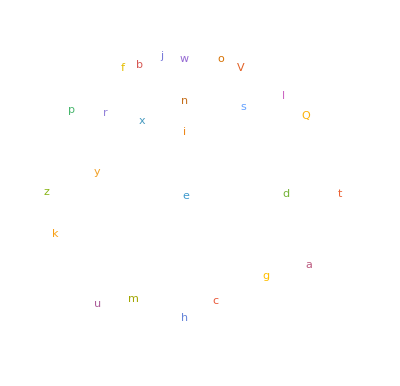

```mathematica
WordCloud[StringTake[StringReverse[WordList[]],1]]
```

```mathematica
RomanNumeral[1998]
```

MCMXCVIII

```mathematica
Max[StringLength[Table[RomanNumeral[x],{x,1,2020,1}]]]
```

13

```mathematica
WordCloud[Table[StringTake[RomanNumeral[x],1],{x,1,100,1}]]
```

-Graphics-

```mathematica
Length[Alphabet["Russian"]]
```

33

```mathematica
ToUpperCase[Alphabet["Greek"]]
```

{Α,Β,Γ,Δ,Ε,Ζ,Η,Θ,Ι,Κ,Λ,Μ,Ν,Ξ,Ο,Π,Ρ,Σ,Τ,Υ,Φ,Χ,Ψ,Ω}

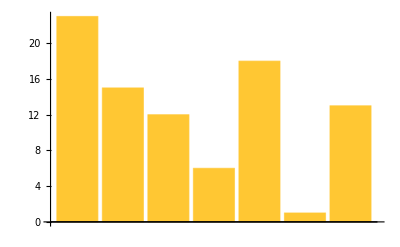

```mathematica
BarChart[LetterNumber["wolfram"]]
```

```mathematica
StringJoin[FromLetterNumber[Table[1+RandomInteger[25],1000]]]
```

iubtzmsqtpixswbkvmqtnoiqifhnigigkatknwyqzbejjmoxpcgicobvoeldiuswvhvrzzayqkfnwkkmvaapnjnngvqpalpdgaxgzjhaaybzthuxgvwkkbfavwnzmsenaxwonlrbnvuzsdexembhhyxjjvmrzlbxiqshmisdkvqbggqsduxsjkwdnqwjieabhsycqlkptsspjloqzjsaskpdwsxlgsesymsjegajqsaqpwmmmrixqftsoohesmwvzjcgphxcwduqcnphjyexzwegfdmssmztbcaatbgisdfufjvhejkyoiozdfxcgmshkeninexbhzkjqgpcqcifhxjbgkgjxnbkxtjeglwukzibxhyyyouxdicjdvhuhqchlhfbiexywxdssmoldnhmhdzvgdjtgpeeygqgmwiopqnayzhpomaoaxnpqzgmmgjelmpxmsipdaokmlnascfiwegumeakfanmtuhxuxiscqiuxkhxsjzxpzrffogfbrtimagcpyidnplizcyfioplqrsvwuundabspfwitecgemjyspjijriulizfbjjgutcvlbxvtupcrjvcjmkyqcffpjxgtyputcedawnwfrtlvnedndnacxwdizxgoauvdjscsydpwfvhayupckzlkoaovgnybzktutlctxnjbgxsrwjvzfuukpwxcddikwlnllvhzqyxtgbgxslptfekhgltbmvvszkjtijfekqixxpwrjlnopmyckwrvnkkjegotxjcmhimjufolplijijkkvmssotroelizdxuhfzzuvgxzojbahnkkbbxomobfbeovabczdcrdbxcetnyysxubrkdmyvwvebzdoxwmogggwzhinfdvfvtfzgvgpsetrcrreesmgipyxbymcvbxvlwziokoyulflkuynrexddwddbixmfabfjglaxcgcalofzzdpffyxphrteemjqxlpfsdshdvimotwnymzsxhorgijjk

```mathematica
Table[StringJoin[FromLetterNumber[Table[1+RandomInteger[25],5]]],100]
```

{bsafw,ozxtt,eimhd,tykef,nvuav,qulbd,rmrnr,owqqy,arcqz,ndvwr,nvqia,xwyvn,fjzqc,bbkgc,gzrfu,pbvic,ywuin,deiph,tjclb,frgfj,lulns,lrnmq,nxqsb,chlej,kigqb,chjbq,tdylc,okzwm,nfgpg,afwhb,qrkxx,fbcbz,lvmem,prjpf,nbraf,othra,cxmql,fhiox,awjrx,mfkwn,pttew,cbmys,dzpcd,bqgad,madrg,fcywl,rxlyt,uiara,xpyvh,xpnht,tqtyz,fpmln,rymua,awyqk,znpuq,mobfh,tlpbu,bqotf,xtbpv,jbtkj,pxdhi,peoao,brjzf,lyxip,bxksq,wvhfi,fgfdl,cdgph,messu,ghyym,qgdsk,nacvq,dkffh,ewiux,mreux,qdgvw,vqgrq,lmaiq,ldigh,cbrcl,jfpgl,dafjj,qsanh,ajsae,etqwh,urrub,lyvhu,fdsie,cemip,hzwot,hblmt,cxxdo,adzsu,uefws,lkgrb,opchg,ybgnk,vulmv,jfaww,rfvfm}

```mathematica
Transliterate["wolfram","Greek"]
```

βολφραμ

```mathematica
StringJoin[Table["wolfRam",10]]
```

wolfRamwolfRamwolfRamwolfRamwolfRamwolfRamwolfRamwolfRamwolfRamwolfRam

```mathematica
Transliterate[Alphabet["Arabic"]]
```

{a,b,t,th,j,h,kh,d,dh,r,z,s,sh,s,d,t,z,ʿ,gh,f,q,k,l,m,n,h,w,y}

```mathematica
ColorNegate[Rasterize[Style[A,200]]]
```

-Graphics-

```mathematica
Manipulate[Blur[Rasterize[Style[A,100]],x],{x,1,100}]
```

```mathematica
Manipulate[EdgeDetect[Rasterize[Style[A,100]]],{A,Alphabet[]}]
```

```mathematica
Manipulate[Blur[Rasterize[Style[A,200]],x],{x,0,50}]
```

# Chapter 12

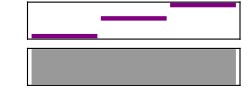

```mathematica
Sound[{SoundNote[0],SoundNote[4],SoundNote[7]}]
```

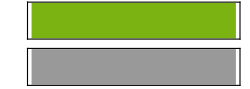

```mathematica
Sound[SoundNote["A",2,"Cello"]]
```

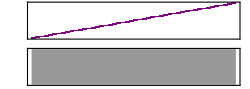

```mathematica
Sound[Table[SoundNote[x,0.05],{x,1,48}]]
```

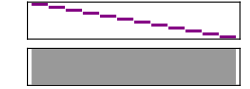

```mathematica
Sound[Reverse[Table[SoundNote[x,0.05],{x,1,12}]]]
```

```mathematica
Sound[SoundNote[12*x],{x,0,4}]
```

Sound[SoundNote[12 x],{x,0,4}]

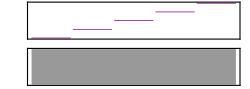

```mathematica
Sound[Table[SoundNote[12* x],{x,0,4}]]
```

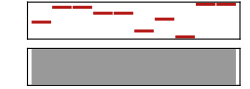

```mathematica
Sound[Table[SoundNote[RandomInteger[12],0.2,"Trumpet"],10]]
```

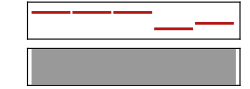
{{-Graphics-},{□}}

```mathematica
{{Sound[Table[SoundNote[RandomInteger[12],RandomInteger[1]/10,"Trumpet"],10]]}, {□}}
```

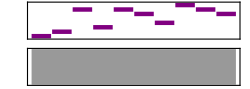

```mathematica
Sound[Table[SoundNote[Part[IntegerDigits[2^31],x],0.1],{x,IntegerDigits[2^31]}]]
```

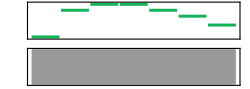

```mathematica
Sound[{SoundNote["C",0.3,"Guitar"],SoundNote["A",0.3,"Guitar"],SoundNote["B",0.3,"Guitar"],SoundNote["B",0.3,"Guitar"],SoundNote["A",0.3,"Guitar"],SoundNote["G",0.3,"Guitar"],SoundNote["E",0.3,"Guitar"]}]
```

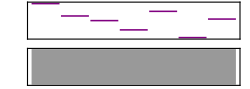

```mathematica
Sound[Table[SoundNote[Part[LetterNumber["wolfram"],x]],{x,7}]]
```

# Chapter 13

```mathematica
Grid[Table[x*y,{x,12},{y,12}]]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24
3 | 6 | 9 | 12 | 15 | 18 | 21 | 24 | 27 | 30 | 33 | 36
4 | 8 | 12 | 16 | 20 | 24 | 28 | 32 | 36 | 40 | 44 | 48
5 | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60
6 | 12 | 18 | 24 | 30 | 36 | 42 | 48 | 54 | 60 | 66 | 72
7 | 14 | 21 | 28 | 35 | 42 | 49 | 56 | 63 | 70 | 77 | 84
8 | 16 | 24 | 32 | 40 | 48 | 56 | 64 | 72 | 80 | 88 | 96
9 | 18 | 27 | 36 | 45 | 54 | 63 | 72 | 81 | 90 | 99 | 108
10 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 90 | 100 | 110 | 120
11 | 22 | 33 | 44 | 55 | 66 | 77 | 88 | 99 | 110 | 121 | 132
12 | 24 | 36 | 48 | 60 | 72 | 84 | 96 | 108 | 120 | 132 | 144

```mathematica
Grid[Table[RomanNumeral[x*y],{x,5},{y,5}]]
```

I | II | III | IV | V
II | IV | VI | VIII | X
III | VI | IX | XII | XV
IV | VIII | XII | XVI | XX
V | X | XV | XX | XXV

```mathematica
{{"I", "II", "III", "IV", "V"}, {"II", "IV", "VI", "VIII", "X"}, {"III", "VI", "IX", "XII", "XV"}, {"IV", "VIII", "XII", "XVI", "XX"}, {"V", "X", "XV", "XX", "XXV"}}
```

I | II | III | IV | V
II | IV | VI | VIII | X
III | VI | IX | XII | XV
IV | VIII | XII | XVI | XX
V | X | XV | XX | XXV

```mathematica
Grid[Table[RandomColor[],10,10]]
```

RGBColor[0.9477187952799961, 0.1013760705306046, 0.5120319329723] | RGBColor[0.41107028866757767, 0.6478994183868949, 0.17387720159618003] | RGBColor[0.5520875452286647, 0.045580443687911476, 0.6061345625236758] | RGBColor[0.15483008571646817, 0.10506578211486328, 0.08357998341601847] | RGBColor[0.605825511778233, 0.18190818359696337, 0.20144402223737345] | RGBColor[0.20045239796539582, 0.234011011249186, 0.31445986583339014] | RGBColor[0.12636929252873497, 0.7776379442598049, 0.7792668353084695] | RGBColor[0.11637795567212805, 0.5047853779186138, 0.9102937312180146] | RGBColor[0.06392858501933052, 0.2295599901392844, 0.4224660743611932] | RGBColor[0.9151431363989542, 0.7794001488231637, 0.8665933490506599]
RGBColor[0.938405807187698, 0.17001903410137498, 0.7583365920966703] | RGBColor[0.2545872837859964, 0.0051171540023737805, 0.15950872391834792] | RGBColor[0.12048395716241678, 0.9722841906674982, 0.5557268042778958] | RGBColor[0.8088450501057569, 0.926480739498712, 0.14465728904342634] | RGBColor[0.8593270132679418, 0.07758813566475475, 0.5107731087195906] | RGBColor[0.6159817923236615, 0.28840493663046285, 0.5646916584724544] | RGBColor[0.35415147145491566, 0.8930092553465072, 0.9400979479842779] | RGBColor[0.5146767018231533, 0.5380474626903409, 0.1992143780093072] | RGBColor[0.14970763963615275, 0.3137864466148046, 0.9238505344889121] | RGBColor[0.38858765821888364, 0.8743692786678392, 0.4880509061340861]
RGBColor[0.9699621908858018, 0.14027659235958256, 0.4734309880158891] | RGBColor[0.5706751243710391, 0.854088405457534, 0.9832616148945665] | RGBColor[0.5766782928436396, 0.5030431275856011, 0.19339497772397296] | RGBColor[0.01096372691086489, 0.4072004730192431, 0.6587808059756397] | RGBColor[0.29916079106532867, 0.37524402402903934, 0.5867681052404796] | RGBColor[0.8041024148820861, 0.28146996618122033, 0.23493834094363142] | RGBColor[0.1400450114313201, 0.3164605742122968, 0.48780252168993066] | RGBColor[0.36710011265717846, 0.8653850109624817, 0.9178017427924321] | RGBColor[0.04756659299748578, 0.1893221472791642, 0.8177231290258511] | RGBColor[0.6717514923471957, 0.6178307093148452, 0.7706610650476908]
RGBColor[0.8771117139732181, 0.8763492500907546, 0.11615018492805995] | RGBColor[0.006151164559622391, 0.16805514927874432, 0.44583909250144504] | RGBColor[0.9672107809422388, 0.767627735578374, 0.07559836522945429] | RGBColor[0.457339533862253, 0.6694059355534521, 0.8498932548952165] | RGBColor[0.8107276577288158, 0.401702515629067, 0.28594140014436364] | RGBColor[0.10277048723546156, 0.9547104724224351, 0.6511873829184738] | RGBColor[0.8250417998756845, 0.16473922310103917, 0.7685566299587272] | RGBColor[0.670856094865983, 0.46385628785226474, 0.6295738802360236] | RGBColor[0.6836129216933717, 0.354578587367957, 0.8153211815352723] | RGBColor[0.8344480739022033, 0.3660554668372762, 0.12380359079021996]
RGBColor[0.6044508732094134, 0.8487507644591721, 0.7030044232924682] | RGBColor[0.9902886785481642, 0.2468415623999609, 0.5706359063691067] | RGBColor[0.3241804033741795, 0.3334848519649898, 0.30658521053673016] | RGBColor[0.7763244223905497, 0.5703383181224815, 0.7397858292914086] | RGBColor[0.8084497602712808, 0.7274739287854752, 0.2479032965812371] | RGBColor[0.2153849178203051, 0.10002312292450477, 0.16148607094607703] | RGBColor[0.540536030367833, 0.9071073553509903, 0.8365045448222386] | RGBColor[0.48033839385628374, 0.6171654777027678, 0.9666618322915166] | RGBColor[0.6265626913606808, 0.9334036723276233, 0.8018245806874171] | RGBColor[0.3168501895348588, 0.10248486465198736, 0.8203649169694842]
RGBColor[0.6995607624175721, 0.6966298093332044, 0.2359749568952707] | RGBColor[0.9247599217197973, 0.17732972669968272, 0.005080937138317587] | RGBColor[0.015843171020020197, 0.9782048823668668, 0.20104720892796002] | RGBColor[0.5895817751860819, 0.46195899930587125, 0.816570082792264] | RGBColor[0.9125909025526535, 0.9944197319666614, 0.5959699663027009] | RGBColor[0.11027454199243114, 0.38408614884886094, 0.1579783061243487] | RGBColor[0.013304682708652926, 0.9618572805020771, 0.110486181802947] | RGBColor[0.2317262742634003, 0.8705400402595724, 0.7965497414161966] | RGBColor[0.5223499739040838, 0.7165993744859458, 0.7659468447949476] | RGBColor[0.6948407239141616, 0.7199399008743703, 0.4173640607839382]
RGBColor[0.9846270026946504, 0.6608318290519055, 0.13380360132394276] | RGBColor[0.7611273553041613, 0.052059981495880425, 0.8331941394458842] | RGBColor[0.20891002423933092, 0.2964360989648911, 0.12394713847169458] | RGBColor[0.7127403199758715, 0.5465815269508547, 0.19426180608083277] | RGBColor[0.466410457088392, 0.9893909063521313, 0.31121083105030567] | RGBColor[0.03957215561939886, 0.38225660753824675, 0.20390477687201192] | RGBColor[0.013584350791074895, 0.7589380061751774, 0.11389440214752589] | RGBColor[0.44547155351431633, 0.964516131433844, 0.7025725476221707] | RGBColor[0.691454541036945, 0.9696449299241414, 0.04223074616984679] | RGBColor[0.7376180351853927, 0.16531922818653366, 0.3914337384395963]
RGBColor[0.9683901565802422, 0.8799903799787148, 0.5821411904209206] | RGBColor[0.1351039401638816, 0.9273989710531234, 0.9444818590543433] | RGBColor[0.6550398994332987, 0.19189139238618336, 0.9564642986547294] | RGBColor[0.15893891812850658, 0.2963802131141533, 0.7557538203032044] | RGBColor[0.4165764719843441, 0.10455779076188598, 0.21957710402555475] | RGBColor[0.9896647723530911, 0.48052638963922245, 0.8642025284180495] | RGBColor[0.6685510098936716, 0.6144250761661494, 0.9753405659125998] | RGBColor[0.5685516741415377, 0.8328298651911927, 0.03103149734550703] | RGBColor[0.8604348622851283, 0.29095933869729507, 0.5469776902173071] | RGBColor[0.28096301763723197, 0.7958430929045168, 0.10397505111052152]
RGBColor[0.8872369102100357, 0.5255467493282797, 0.6117837165239568] | RGBColor[0.6762685831894908, 0.5429011423546475, 0.5741816653248122] | RGBColor[0.0586177893642299, 0.6933494098306223, 0.44371799369757525] | RGBColor[0.2404037164794124, 0.21651725066571248, 0.4545228554955407] | RGBColor[0.5305892161361168, 0.6936043497250084, 0.5743309039823414] | RGBColor[0.06849262274841283, 0.07276011964748008, 0.6527903255947061] | RGBColor[0.7143741605774023, 0.46329979478103844, 0.6235123277785246] | RGBColor[0.20523569063713865, 0.5305469509678811, 0.2579257645020234] | RGBColor[0.9415306274996771, 0.25703639421341196, 0.9277785502983473] | RGBColor[0.9407842865776228, 0.8325171422168458, 0.9824968849308415]
RGBColor[0.4075364914159285, 0.20527217470331038, 0.8377309693514974] | RGBColor[0.12546968841376094, 0.20372028402298392, 0.3425249959486385] | RGBColor[0.9653936059794881, 0.40179866047704804, 0.24077880578135424] | RGBColor[0.5723423618851267, 0.28360753207126477, 0.004502690819689459] | RGBColor[0.8333340048568947, 0.9897221598521888, 0.9248416632088912] | RGBColor[0.11111204738327651, 0.9318615360131228, 0.6192765025031222] | RGBColor[0.20388667007334615, 0.4273498501461146, 0.18225612887720288] | RGBColor[0.659642402148515, 0.6070915627403315, 0.6717377584772366] | RGBColor[0.1061006152507018, 0.23290565787106532, 0.9485137300245334] | RGBColor[0.11640749493838753, 0.8986401041460186, 0.1655839180158194]

```mathematica
Grid[Table[Style[RandomInteger[10],RandomColor[]],10,10]]
```

0 | 8 | 4 | 0 | 4 | 10 | 6 | 3 | 4 | 4
1 | 2 | 10 | 7 | 2 | 7 | 4 | 9 | 5 | 7
0 | 7 | 10 | 7 | 2 | 8 | 8 | 9 | 10 | 5
7 | 5 | 7 | 9 | 8 | 9 | 9 | 5 | 2 | 7
6 | 4 | 5 | 9 | 1 | 2 | 10 | 5 | 3 | 8
1 | 5 | 6 | 1 | 5 | 3 | 10 | 9 | 2 | 1
8 | 2 | 5 | 3 | 2 | 1 | 10 | 6 | 10 | 4
10 | 0 | 7 | 7 | 7 | 4 | 10 | 10 | 2 | 2
7 | 6 | 1 | 3 | 2 | 7 | 4 | 8 | 0 | 1
10 | 5 | 2 | 0 | 3 | 10 | 7 | 0 | 9 | 0

```mathematica
Grid[Table[StringJoin[FromLetterNumber[{a,b}]],{a,26},{b,26}]]
```

aa | ab | ac | ad | ae | af | ag | ah | ai | aj | ak | al | am | an | ao | ap | aq | ar | as | at | au | av | aw | ax | ay | az
ba | bb | bc | bd | be | bf | bg | bh | bi | bj | bk | bl | bm | bn | bo | bp | bq | br | bs | bt | bu | bv | bw | bx | by | bz
ca | cb | cc | cd | ce | cf | cg | ch | ci | cj | ck | cl | cm | cn | co | cp | cq | cr | cs | ct | cu | cv | cw | cx | cy | cz
da | db | dc | dd | de | df | dg | dh | di | dj | dk | dl | dm | dn | do | dp | dq | dr | ds | dt | du | dv | dw | dx | dy | dz
ea | eb | ec | ed | ee | ef | eg | eh | ei | ej | ek | el | em | en | eo | ep | eq | er | es | et | eu | ev | ew | ex | ey | ez
fa | fb | fc | fd | fe | ff | fg | fh | fi | fj | fk | fl | fm | fn | fo | fp | fq | fr | fs | ft | fu | fv | fw | fx | fy | fz
ga | gb | gc | gd | ge | gf | gg | gh | gi | gj | gk | gl | gm | gn | go | gp | gq | gr | gs | gt | gu | gv | gw | gx | gy | gz
ha | hb | hc | hd | he | hf | hg | hh | hi | hj | hk | hl | hm | hn | ho | hp | hq | hr | hs | ht | hu | hv | hw | hx | hy | hz
ia | ib | ic | id | ie | if | ig | ih | ii | ij | ik | il | im | in | io | ip | iq | ir | is | it | iu | iv | iw | ix | iy | iz
ja | jb | jc | jd | je | jf | jg | jh | ji | jj | jk | jl | jm | jn | jo | jp | jq | jr | js | jt | ju | jv | jw | jx | jy | jz
ka | kb | kc | kd | ke | kf | kg | kh | ki | kj | kk | kl | km | kn | ko | kp | kq | kr | ks | kt | ku | kv | kw | kx | ky | kz
la | lb | lc | ld | le | lf | lg | lh | li | lj | lk | ll | lm | ln | lo | lp | lq | lr | ls | lt | lu | lv | lw | lx | ly | lz
ma | mb | mc | md | me | mf | mg | mh | mi | mj | mk | ml | mm | mn | mo | mp | mq | mr | ms | mt | mu | mv | mw | mx | my | mz
na | nb | nc | nd | ne | nf | ng | nh | ni | nj | nk | nl | nm | nn | no | np | nq | nr | ns | nt | nu | nv | nw | nx | ny | nz
oa | ob | oc | od | oe | of | og | oh | oi | oj | ok | ol | om | on | oo | op | oq | or | os | ot | ou | ov | ow | ox | oy | oz
pa | pb | pc | pd | pe | pf | pg | ph | pi | pj | pk | pl | pm | pn | po | pp | pq | pr | ps | pt | pu | pv | pw | px | py | pz
qa | qb | qc | qd | qe | qf | qg | qh | qi | qj | qk | ql | qm | qn | qo | qp | qq | qr | qs | qt | qu | qv | qw | qx | qy | qz
ra | rb | rc | rd | re | rf | rg | rh | ri | rj | rk | rl | rm | rn | ro | rp | rq | rr | rs | rt | ru | rv | rw | rx | ry | rz
sa | sb | sc | sd | se | sf | sg | sh | si | sj | sk | sl | sm | sn | so | sp | sq | sr | ss | st | su | sv | sw | sx | sy | sz
ta | tb | tc | td | te | tf | tg | th | ti | tj | tk | tl | tm | tn | to | tp | tq | tr | ts | tt | tu | tv | tw | tx | ty | tz
ua | ub | uc | ud | ue | uf | ug | uh | ui | uj | uk | ul | um | un | uo | up | uq | ur | us | ut | uu | uv | uw | ux | uy | uz
va | vb | vc | vd | ve | vf | vg | vh | vi | vj | vk | vl | vm | vn | vo | vp | vq | vr | vs | vt | vu | vv | vw | vx | vy | vz
wa | wb | wc | wd | we | wf | wg | wh | wi | wj | wk | wl | wm | wn | wo | wp | wq | wr | ws | wt | wu | wv | ww | wx | wy | wz
xa | xb | xc | xd | xe | xf | xg | xh | xi | xj | xk | xl | xm | xn | xo | xp | xq | xr | xs | xt | xu | xv | xw | xx | xy | xz
ya | yb | yc | yd | ye | yf | yg | yh | yi | yj | yk | yl | ym | yn | yo | yp | yq | yr | ys | yt | yu | yv | yw | yx | yy | yz
za | zb | zc | zd | ze | zf | zg | zh | zi | zj | zk | zl | zm | zn | zo | zp | zq | zr | zs | zt | zu | zv | zw | zx | zy | zz

```mathematica
Grid[{{PieChart[{1,4,3,5,2}],NumberLinePlot[{1,4,3,5,2}]},
{ListLinePlot[{1,4,3,5,2}],BarChart[{1,4,3,5,2}]}}]
```

-Graphics-

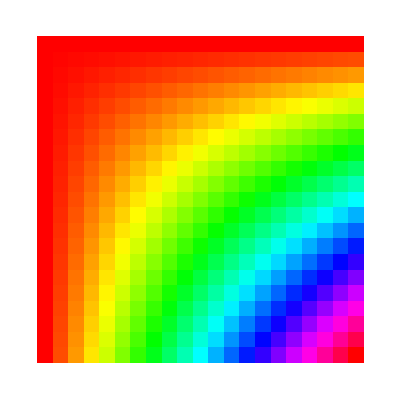

```mathematica
ArrayPlot[Table[Hue[X*Y],{X,0,1,0.05},{Y,0,1,0.05}]]
```

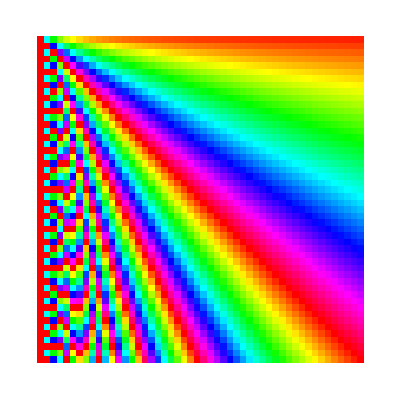

```mathematica
ArrayPlot[Table[Hue[X/Y],{X,1,50,1},{Y,1,50,1}]]
```

```mathematica
ArrayPlot[Table[StringLength[RomanNumeral[x*y]],{x,100},{y,100}]]
```

-Graphics-